# Hints for a luminosity transition in the Cepheid SnIa calibrator data - Leandros Perivolaropoulos and Foteini Skara - ΔAIC-ΔBIC (all cases)

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol];
```

## Parameters - Data - Matrix of Measurements Y - Matrix of Parameters X

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]
```

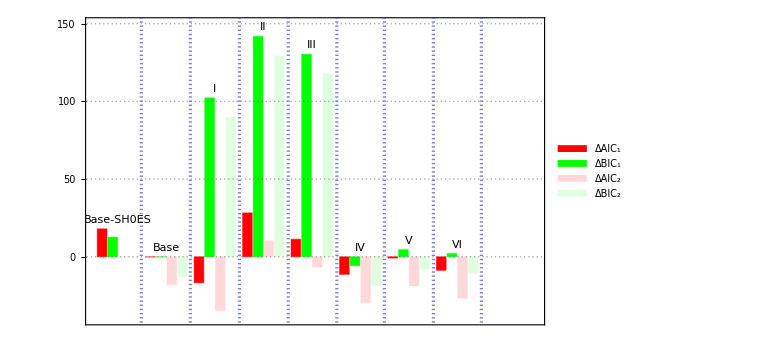

```mathematica
color=Darker[Blue];
figbaric=BarChart[{{17.97,12.57,0,0},{0,0,-17.97,-12.57},{-16.76,102.24,-34.73,89.67},{28.22,141.81,10.25,129.24},{11.27,130.27,-6.7,117.7},{-11.36,-5.75,-29.33,-18.32},{-0.84,4.57,-18.81,-8},{-8.73,2.09,-26.7,-10.48}},ChartStyle->{Red,Green,LightRed,LightGreen},ChartLabels->{Placed[{"Base-SH0ES","Base","I","II","III","IV","V","VI"},Above],{" "," "," "," "}},ChartLegends->Placed[{"ΔAIC_1 ","ΔBIC_1","ΔAIC_2","ΔBIC_2"},{Right,Center}],BarSpacing->{0.1,0.7},PlotRange->{{0.6,42},{-40,150}},GridLines->{{{5,Directive[color,Thickness[0.004]]},{9.6,Directive[color,Thickness[0.004]]},{14.2,Directive[color,Thickness[0.004]]},{18.78,Directive[color,Thickness[0.004]]},{23.34,Directive[color,Thickness[0.004]]},{27.8,Directive[color,Thickness[0.004]]},{32.4,Directive[color,Thickness[0.004]]},{36.9,Directive[color,Thickness[0.004]]}},{0,50,100,150}},PlotTheme->"Business",LabelStyle->Directive[Bold,FontFamily->"Times New Roman",12,Black],Frame->True,ImageSize->Large,BaseStyle->Directive[Bold,FontFamily->"Times New Roman",12,Black],FrameStyle -> Directive[Black, Thick]]
```

```mathematica
Export[NotebookDirectory[]<>"figbaric.pdf",figbaric,ImageResolution->1000];
```